```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
ρ=Take[#[EntityProperty["Element","AtomicSymbol"]]->#[EntityProperty["Element","Resistivity"]]&/@EntityList@EntityClass["Element",All]//Association//Sort//DeleteMissing,{1,-10}]//Dataset
```

## Measurements of the setup

```mathematica
L=10^-2{20,40,60}&/@Range[1,6]//N; (* Lengths of the wires (cm) *)
r=1/2 10^-3{1.00,0.74,0.71,0.51,0.35,0.52}; (* Radii of the wires (mm) *)
```

## 2-probes measurement of resistivity

```mathematica
Subscript[V, 2]=10^-3{{0.381,0.515,0.62},{0.52,0.756,1.015},{0.5,0.763,1.026},{0.774,1.302,1.838},{1.29,2.338,3.378},{0.382,0.44,0.524}};
```

```mathematica
Subscript[F, 2]=LinearModelFit[Transpose[#],x,x]&/@Transpose[{L,Subscript[V, 2]}];
```

```mathematica
Plot[#["BestFit"]&/@Subscript[F, 2]//Evaluate,{x,0,1},PlotLabels->"Expressions",ImageSize->Large]//Show[#,ListPlot[Transpose[#]&/@Transpose[{L,Subscript[V, 2]}]]]&
```

-Graphics-

```mathematica
Subscript[α, 2]=#["BestFitParameters"][[2]]&/@Subscript[F, 2];
```

```mathematica
Subscript[ρ, 2]=#1(π#2^2)/10^-3&@@@Transpose[{Subscript[α, 2],r}];
```

```mathematica
θ=CharacterRange["A","F"];
Subscript[μ, 2]=#1->#2 Quantity[, "Meters" "Ohms"]&@@@Transpose[{θ,Subscript[ρ, 2]}]//Association//Dataset
```

```mathematica
ListPlot[{Subscript[μ, 2],ρ},PlotRange->Automatic,ImageSize->Large,PlotLabel->"2-probes aquisition method"]
```

-Graphics-

```mathematica
Nearest[ρ//Normal,#,20]&/@Values[Subscript[μ, 2]]//Normal//#1->#2&@@@Transpose[{θ,#}]&//Association//Dataset
```

## 4-probes measurement of resistivity

```mathematica
Subscript[V, 4]=10^-3{{0.05,0.212,0.335},{0.18,0.45,0.711},{0.193,0.44,0.712},{0.453,0.969,1.5},{0.970,2.02,3.063},{0.008,0.08,0.18}};
```

```mathematica
Subscript[F, 4]=LinearModelFit[Transpose[#],x,x]&/@Transpose[{L,Subscript[V, 4]}];
```

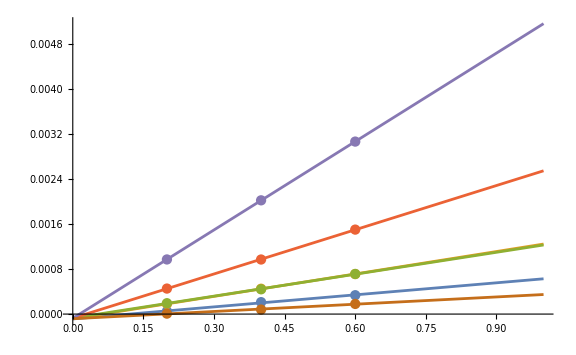

```mathematica
Plot[#["BestFit"]&/@Subscript[F, 4]//Evaluate,{x,0,1},ImageSize->Large]//Show[#,ListPlot[Transpose[#]&/@Transpose[{L,Subscript[V, 4]}]]]&
```

```mathematica
Subscript[α, 4]=#["BestFitParameters"][[2]]&/@Subscript[F, 4];
```

```mathematica
Subscript[ρ, 4]=#1(π#2^2)/10^-3&@@@Transpose[{Subscript[α, 4],r}];
```

```mathematica
Subscript[μ, 4]=#1->#2 Quantity[, "Meters" "Ohms"]&@@@Transpose[{θ,Subscript[ρ, 4]}]//Association//Dataset
```

```mathematica
ListPlot[{Subscript[μ, 4],ρ},PlotRange->Automatic,ImageSize->Large,PlotLabel->"4-probes aquisition method"]
```

-Graphics-

```mathematica
Nearest[ρ//Normal,#,20]&/@Values[Subscript[μ, 4]]//Normal//#1->#2&@@@Transpose[{θ,#}]&//Association//Dataset
```

## Additional stuff on the wire measurements

```mathematica
PercentForm[(Subscript[ρ, 4]-Subscript[ρ, 2])/Subscript[ρ, 2]]
```

{19.25%,7.273%,-1.331%,-1.598%,0.2395%,21.13%}

## First part of the experiment with the thermistor

```mathematica
δ=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Mathematica/RT/Dati.txt","Table","HeaderLines"->6,"FieldSeparators"->"\t","NumberPoint"->",",CharacterEncoding->"UTF8"]//Dataset//#[All,Range[1,12]]&;
δ=δ[All,<|"t (s)"->1,"V_1 (V)"->2,"V_2 (V)"->3,"V_3 (V)"->4,"V_4 (V)"->5,"R_1 (Ω)"->6,"R_2 (Ω)"->7,"R_3 (Ω)"->8,"T (K)"->9,"R_1/(R_(1, 0))"->10,"R_2/(R_(2, 0))"->11,"R_3/(R_(3, 0))"->12|>]
```

Dataset[<>]

```mathematica
With[{τ={"R_1/(R_(1, 0))","R_2/(R_(2, 0))","R_3/(R_(3, 0))"}},ListLinePlot[Transpose[{δ[All,"T (K)"],δ[All,#]}//Normal]&/@τ,PlotRange->All,PlotLabels->τ,AxesLabel->{"T (K)","R (Ω)"}]]
```

-Graphics-

```mathematica
With[{τ={"R_1/(R_(1, 0))","R_2/(R_(2, 0))","R_3/(R_(3, 0))"}},ListLinePlot[Transpose[{δ[All,"t (s)"],δ[All,#]}//Normal]&/@τ,PlotRange->All,PlotLabels->τ,AxesLabel->{"t (s)"}]]
```

-Graphics-

```mathematica
With[{τ={"V_1 (V)","V_2 (V)","V_3 (V)","V_4 (V)"}},ListLinePlot[Transpose[{δ[All,"t (s)"],δ[All,#]}//Normal]&/@τ,PlotRange->All,PlotLabels->τ,AxesLabel->{"t (s)","V (V)"}]]
```

-Graphics-